```mathematica
dataWithError= ErrorListPlot[{{21.8*10^(-9),.83}, ErrorBar[0.1*10^(-9),0.01]},{{23.5*10^(-9),1.385},ErrorBar[0.1*10^(-9),0.01]},{{25.1*10^(-9),1.87},ErrorBar[0.1*10^(-9),0.01]},{{26.9*10^(-9),2.375},ErrorBar[0.1*10^(-9),0.01]},{{28.1*10^(-9),2.85},ErrorBar[0.1*10^(-9),0.01]},{{29.6*10^(-9),3.345},ErrorBar[0.1*10^(-9),0.01]},{{30.7*10^(-9),3.82},ErrorBar[0.1*10^(-9),0.01]},{{31.8*10^(-9),4.295},ErrorBar[0.1*10^(-9),0.01]},{{32.9*10^(-9),4.795},ErrorBar[0.1*10^(-9),0.01]},{{33.5*10^(-9),5.33},ErrorBar[0.1*10^(-9),0.01]},{{37.7*10^(-9),5.795},ErrorBar[0.1*10^(-9),0.01]},{{39.5*10^(-9),6.34},ErrorBar[0.1*10^(-9),0.01]},{{41.5*10^(-9),6.785},ErrorBar[0.1*10^(-9),0.01]},{{43.3*10^(-9),7.36},ErrorBar[0.1*10^(-9),0.01]},{{44.8*10^(-9),7.87},ErrorBar[0.1*10^(-9),0.01]}, PlotStyle->{Black}];
```

```mathematica
data = List[{21.8*10^(-9),.83},{23.5*10^(-9),1.385},{25.1*10^(-9),1.87},{26.9*10^(-9),2.375},{28.1*10^(-9),2.85},{29.6*10^(-9),3.345},{30.7*10^(-9),3.82},{31.8*10^(-9),4.295},{32.9*10^(-9),4.795},{33.5*10^(-9),5.33},{37.7*10^(-9),5.795},{39.5*10^(-9),6.34},{41.5*10^(-9),6.785},{43.3*10^(-9),7.36},{44.8*10^(-9),7.87}];
fit = LinearModelFit[data,x,x];
```

```mathematica
fit["ParameterTable"]
```

```mathematica
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {1, -5.613450050368471, 0.3478564435830345, -16.13726051053736, 5.585910588781752*^-10}, {x, 3.04150704616929*^8, 1.0396987708465692*^7, 29.2537332105602, 3.0003696784968506*^-13}}
```

```mathematica
dataMinusOutliers = List[{21.8*10^(-9),.83},{23.5*10^(-9),1.385},{25.1*10^(-9),1.87},{26.9*10^(-9),2.375},{28.1*10^(-9),2.85},{29.6*10^(-9),3.345},{30.7*10^(-9),3.82},{31.8*10^(-9),4.295},{37.7*10^(-9),5.795},{39.5*10^(-9),6.34},{41.5*10^(-9),6.785},{43.3*10^(-9),7.36},{44.8*10^(-9),7.87}];
fitWithoutOutliers = LinearModelFit[dataMinusOutliers, x, x]
```

```mathematica
FittedModel[-5.6689952563648225+3.031273587856297*^8 x]
fit["ParameterTable"]
```

FittedModel[-5.669+3.03127×10^8 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -5.61345 | 0.347856 | -16.1373 | 5.58591×10^-10
x | 3.04151×10^8 | 1.0397×10^7 | 29.2537 | 3.00037×10^-13

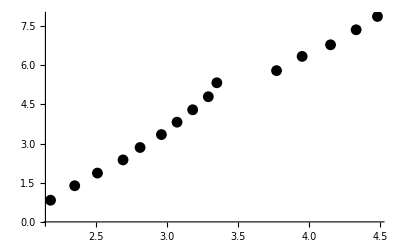

```mathematica
ListPlot[data, PlotStyle->Black]
```

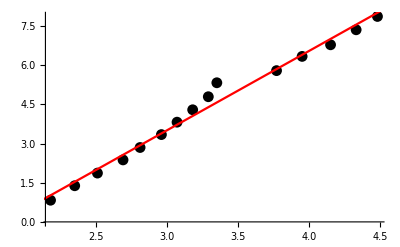

```mathematica
Show[ListPlot[data, PlotStyle->Black], Plot[fit[x],{x,0,50*10^(-9)}, PlotStyle->Red]]
```

Show::gcomb: Could not combine the graphics objects in ….

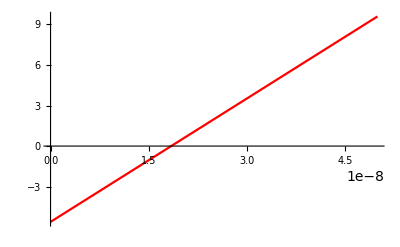
Show[ErrorListPlot[{{2.18×10^-8,0.83},ErrorBar[1.×10^-10,0.01]},{{2.35×10^-8,1.385},ErrorBar[1.×10^-10,0.01]},{{2.51×10^-8,1.87},ErrorBar[1.×10^-10,0.01]},{{2.69×10^-8,2.375},ErrorBar[1.×10^-10,0.01]},{{2.81×10^-8,2.85},ErrorBar[1.×10^-10,0.01]},{{2.96×10^-8,3.345},ErrorBar[1.×10^-10,0.01]},{{3.07×10^-8,3.82},ErrorBar[1.×10^-10,0.01]},{{3.18×10^-8,4.295},ErrorBar[1.×10^-10,0.01]},{{3.29×10^-8,4.795},ErrorBar[1.×10^-10,0.01]},{{3.35×10^-8,5.33},ErrorBar[1.×10^-10,0.01]},{{3.77×10^-8,5.795},ErrorBar[1.×10^-10,0.01]},{{3.95×10^-8,6.34},ErrorBar[1.×10^-10,0.01]},{{4.15×10^-8,6.785},ErrorBar[1.×10^-10,0.01]},{{4.33×10^-8,7.36},ErrorBar[1.×10^-10,0.01]},{{4.48×10^-8,7.87},ErrorBar[1.×10^-10,0.01]},PlotStyle→{-Graphics-}],-Graphics-]

```mathematica
Show[dataWithError, Plot[fit[x],{x,0,50*10^(-9)}, PlotStyle->Red]]
```